# Preparing for Meetings with Stephen Wolfram

## (1) SW Meeting Checklist - Introductory Meeting (Thursday/Friday/Saturday) (5 minutes)

In this meeting, you will talk with Stephen Wolfram in a group of 4-6 other students (plus your advocate, Megan and Rory). He will go around the group and ask each student questions.

He might ask questions like: where are you right now? what are you interested in? tell me about a project you’ve enjoyed in the past?

The goal of this meeting is for him to understand what kinds of projects you would be interested in doing at camp.

he will make decisions on your project based on what you say you are interested in during this meeting (and your written responses to application questions)

If you want to do a project about biology, but when he asks you what you’re interested in, you tell him you like to play chess and ride your bike, he won’t know you want to do a biology project

In order to prepare for this meeting, please think about the following questions in advance and take some notes so you are ready to speak to Stephen:

(he won't ask these questions specifically, but you should still say your answers)

## What topics are you interested in doing a project about? Why?

chemistry/physics

computer science

## What’s the coolest thing you’ve studied so far? Why?

## What are your favorite extra-curricular activities? Why?

## (2) SW Meeting Checklist - Project Allocation (Thursday/Friday/Saturday - 2 hours later) (5-10 minutes)

This meeting is the second time you will meet with Stephen

You will see Stephen one student at a time, with your advocate, Megan, Rory, and someone who will take notes

He will talk you through what he thinks you should do for your project

As you are listening, please think about the following questions:

## Are you excited about this project?

## Does this project feel like it will be hard, but not overwhelmingly so? (hard is good, panic is bad)

## If you don’t like your assigned project, please tell Stephen at the meeting

If you don’t feel comfortable speaking to Stephen, message your advocate, Megan, or Rory during the meeting

if for any reason you didn’t tell someone during the meeting that you don’t like your project, tell your advocate/Megan/Rory immediately. Final deadline for project changing is the end of camp on Saturday July 9th.

## (3) SW Meeting Checklist - Check In (second weekend) (5-10 minutes)

Stephen will ask how your project is going

Tell him what you’ve accomplished and what you have left to do

This is not a technical meeting

do not ask how to code things

do not ask for content insight

Questions you can/should ask:

how can I make this better?

I think I’m going to finish soon, do you have suggestions for other directions?

I think I’m not going to reach the original final goal, do you have suggestions for how I should adjust? (talk to your mentor about this first)

## Favorite bit of code or fun visualization you are excited about

```mathematica
generateAlkylTree[n_Integer]:=Once@Flatten@Table[With[
	{possibleSubBranches = generateAlkylTree/@branching},
	Outer[Tree["C", {##}]&, Sequence@@possibleSubBranches]
], {branching, IntegerPartitions[n - 1, {3}, Range[0, n - 1]]}]

generateAlkylTree[0]:={Tree["H",{}]}
generateAlkylTree[4]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
generateAlkanes[n_Integer]/;n>0:=Molecule/@DeleteDuplicatesBy[
	UndirectedGraph[TreeInsert[#,Atom["H"],{1}]]&/@generateAlkylTree[n],
	CanonicalGraph
]
MoleculePlot[#, ]&/@generateAlkanes[8]//ImageCollage
```

-Graphics-

(Unrelated)

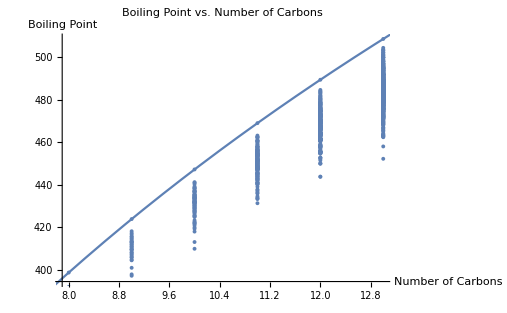

## What have you done to this point?

I have recreated Wiener’s original results (of predicting the boiling point purely based on the structure).

I have optimized a solution to generate isomers of alkanes.

I have created a function to find alkanes whose boiling point is near a given value by brute forcing.

## What is something you are proud of?

The fastest(?) alkane isomer generator in Wolfram Language that I can find online.

## What is your plan for next steps?

(Maybe?) Find the graph with a give Wiener index with something other that exhaustive search/brute forcing. Is this feasible?

Find a new empirical way to approximate the boiling point of unbranched alkanes rather than the century-old Egloff’s equation (doesn’t work well for large molecules).